# Lesson 4: The Limit of a Function

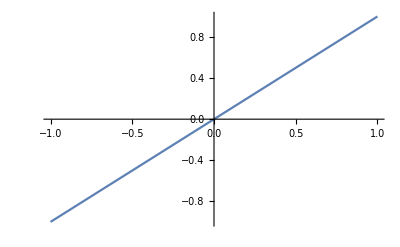

```mathematica
Plot[x,{x,-1,1}]
```

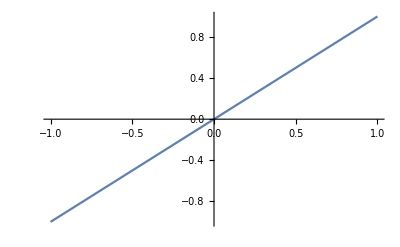

```mathematica
Plot[x^2/x,{x,-1,1}]
```

```mathematica
g[x_]:=x^2/x
```

```mathematica
g[0] //Quiet
```

Indeterminate

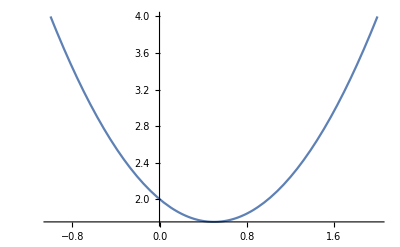

```mathematica
f[x_]:=x^2-x+2
Plot[f[x],{x,-1,2}]
```

```mathematica
limitTablea[function_,xlimit_]:=
Module[{list},list={1,.5,.1,.05,.01,.005,.001};
{TraditionalForm[
Grid[Join[{{"x",function["x"]}},
Transpose[{xlimit-list,function[#]&/@(xlimit-list) //N}]],
Frame->All]],
TraditionalForm[
Grid[Join[{{"x",function["x"]}},
Transpose[{xlimit+list,function[#] &/@(xlimit+list)//N}]],
Frame->All]]}]
limitTablea[f,1] //Quiet
```

{x | x^2-x+2
0 | 2.
0.5 | 1.75
0.9 | 1.91
0.95 | 1.9525
0.99 | 1.9901
0.995 | 1.99503
0.999 | 1.999,x | x^2-x+2
2 | 4.
1.5 | 2.75
1.1 | 2.11
1.05 | 2.0525
1.01 | 2.0101
1.005 | 2.00503
1.001 | 2.001}

```mathematica
Limit[f[x],x->1]
```

2

## Rational Function with a Removable Discontinuity

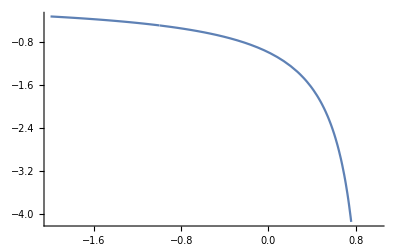

```mathematica
f[x_]:=(x+1)/(x^2-1)

Plot[f[x],{x,-2,1},GridLines->{{-1},{(-1)/2}}]
```

```mathematica
limitTablea[f,-1]
```

{x | (x+1)/(x^2-1)
-2 | -0.333333
-1.5 | -0.4
-1.1 | -0.47619
-1.05 | -0.487805
-1.01 | -0.497512
-1.005 | -0.498753
-1.001 | -0.49975,x | (x+1)/(x^2-1)
0 | -1.
-0.5 | -0.666667
-0.9 | -0.526316
-0.95 | -0.512821
-0.99 | -0.502513
-0.995 | -0.501253
-0.999 | -0.50025}

```mathematica
Limit[f[x],x->-1]
```

-1/2

## Piecewise Function

```mathematica
g[x_]:=Piecewise[{{-.75, x==-1}},
(x+1)/(x^2-1)]
```

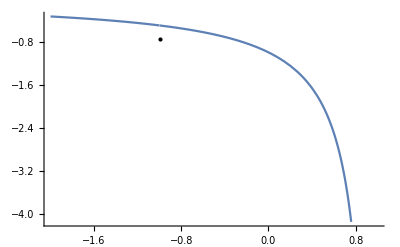

```mathematica
Plot[g[x],{x,-2,1},Sequence[GridLines->{{-1},{-1/2}},
Epilog->{PointSize[Large],Point[{-1,g[-1]}]}]]
```

```mathematica
Limit[g[x],x->-1]
```

-0.5

## Algebraic Function with a Removable Discontinuity

```mathematica
f[x_]:=(Sqrt[x^2+4]-2)/x^2
```

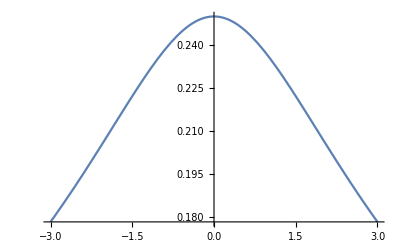

```mathematica
Plot[f[x],{x,-3,3}]
```

```mathematica
Solve[(Sqrt[x^2+4]-2)/x^2==0,x]
```

{}

```mathematica
Limit[f[x],x->0]
```

1/4

```mathematica
limitTablea[f,0] //Quiet
```

{x | (√(x^2+4)-2)/x^2
-1 | 0.236068
-0.5 | 0.246211
-0.1 | 0.249844
-0.05 | 0.249961
-0.01 | 0.249998
-0.005 | 0.25
-0.001 | 0.25,x | (√(x^2+4)-2)/x^2
1 | 0.236068
0.5 | 0.246211
0.1 | 0.249844
0.05 | 0.249961
0.01 | 0.249998
0.005 | 0.25
0.001 | 0.25}

## Trigonometric Function

```mathematica
f[x_]:=Cos[π/x]
```

```mathematica
limitTablea[f,0]
```

{x | cos(π/x)
-1 | -1.
-0.5 | 1.
-0.1 | 1.
-0.05 | 1.
-0.01 | 1.
-0.005 | 1.
-0.001 | 1.,x | cos(π/x)
1 | -1.
0.5 | 1.
0.1 | 1.
0.05 | 1.
0.01 | 1.
0.005 | 1.
0.001 | 1.}

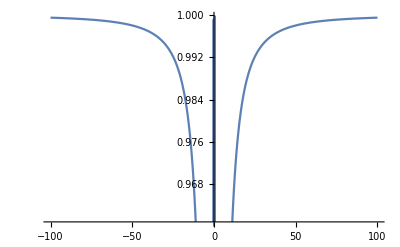

```mathematica
Plot[f[x],{x,-1,1}]
```

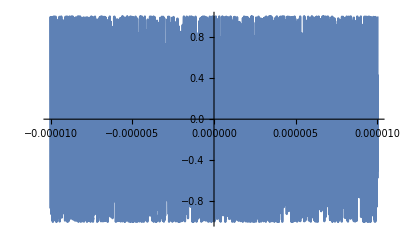

```mathematica
Plot[f[x],{x,-.00001,.00001}]
```

```mathematica
Limit[f[x],x->0]
```

Indeterminate

## Sum of Trigonometric and Polynomial Functions

```mathematica
f[x_]:=4 x^5+3Cos[100x]/200
```

```mathematica
limitTablea[f,0]
```

{x | 4 x^5+3/200 cos(100 x)
-1 | -3.98707
-0.5 | -0.110526
-0.1 | -0.0126261
-0.05 | 0.00425368
-0.01 | 0.00810453
-0.005 | 0.0131637
-0.001 | 0.0149251,x | 4 x^5+3/200 cos(100 x)
1 | 4.01293
0.5 | 0.139474
0.1 | -0.0125461
0.05 | 0.00425618
0.01 | 0.00810453
0.005 | 0.0131637
0.001 | 0.0149251}

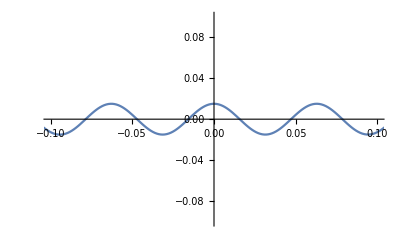

```mathematica
Plot[f[x],{x,-2,2},PlotRange->{{-.1,.1},{-.1,.1}}]
```

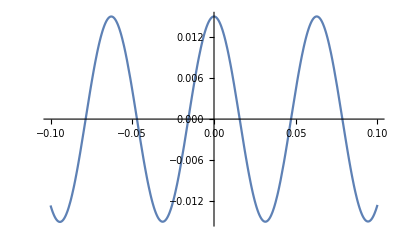

```mathematica
Plot[f[x],{x,-0.1,0.1},PlotRange->All]
```

```mathematica
Limit[f[x],x->0]
```

3/200

## One-Sided Limits

```mathematica
f[x_]:= Piecewise[{{-1,x<0}},1]
```

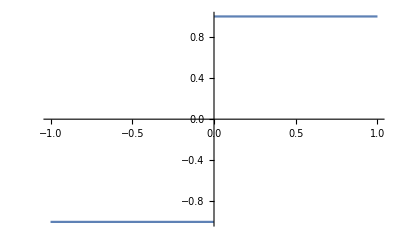

```mathematica
Plot[f[x],{x,-1,1}]
```

```mathematica
{Limit[f[x],x->0,Direction->"FromBelow"],
Limit[f[x],x->0,Direction->"FromAbove"]}
```

{-1,1}

```mathematica
Limit[f[x],x->0]
```

Indeterminate

## General Piecewise Function

```mathematica
f[x_]:=Piecewise[{{4, x==1},{3Cos[x-1],x<1},
{3Sqrt[x],x>1&&x<6}},3x-13]
```

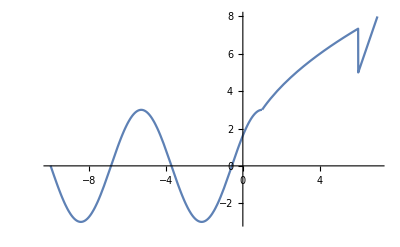

```mathematica
Plot[f[x],{x,-10,7}]
```

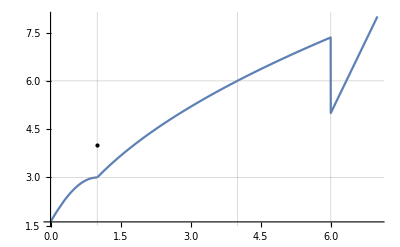

```mathematica
Show[Plot[f[x], {x, 0, 7}, Sequence[
  PlotRange -> All, GridLines -> {{1, 4, 6}, {3, 6}}]], 
 Graphics[{Black, PointSize[Large], Point[{1, f[1]}]}]]
```

```mathematica
Limit[f[x],x->#]&/@{1,4,6}
```

{3,6,Indeterminate}

```mathematica
{Limit[f[x],x->6,Direction->"FromBelow"],
Limit[f[x],x->6,Direction->"FromAbove"]}
```

{3 √6,5}

## Table of Values

```mathematica
f[x_]:=(x^2+2x)/(x^2-4x-5)
```

```mathematica
Grid[Join[{{"x", f[x]}}, 
  Table[{x, 
    f[x]}, {x, {-2, -1.5, -1.1, -1.01, -1.001, -0.999, -0.99, -0.95, \
-0.9, -0.5, 0}}]], Frame -> All]
```

x | (2 x+x^2)/(-5-4 x+x^2)
-2 | 0
-1.5 | -0.230769
-1.1 | -1.62295
-1.01 | -16.6373
-1.001 | -166.639
-0.999 | 166.694
-0.99 | 16.6928
-0.95 | 3.35294
-0.9 | 1.67797
-0.5 | 0.272727
0 | 0

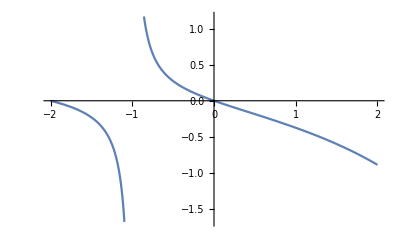

```mathematica
Plot[f[x],{x,-2,2}]
```

```mathematica
{Limit[f[x],x->-1,Direction->"FromBelow"],
Limit[f[x],x->-1,Direction->"FromAbove"]}
```

{-∞,∞}

```mathematica
Limit[f[x],x->-1]
```

Indeterminate

## Vertical Asymptote 1

```mathematica
f[x_]:=1/(x-1)^2
```

```mathematica
limitTablea[f,1]
```

{x | 1/(x-1)^2
0 | 1.
0.5 | 4.
0.9 | 100.
0.95 | 400.
0.99 | 10000.
0.995 | 40000.
0.999 | 1.×10^6,x | 1/(x-1)^2
2 | 1.
1.5 | 4.
1.1 | 100.
1.05 | 400.
1.01 | 10000.
1.005 | 40000.
1.001 | 1.×10^6}

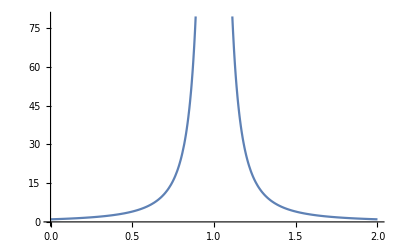

```mathematica
Plot[f[x],{x,0,2}]
```

```mathematica
Limit[f[x],x->1]
```

∞

## Vertical Asymptote 2

```mathematica
f[x_]:=1/x
```

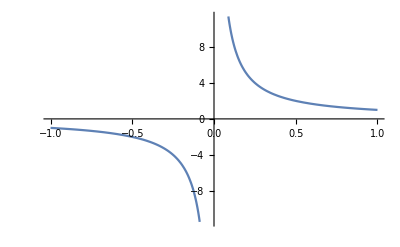

```mathematica
Plot[f[x],{x,-1,1}]
```

```mathematica
{Limit[f[x],x->0,Direction->"FromBelow"],
Limit[f[x],x->0,Direction->"FromAbove"]}
```

{-∞,∞}

```mathematica
Limit[f[x],x->0]
```

Indeterminate

## Finding the Asymptotes of a Function

```mathematica
f[x_]:=Cot[x]
```

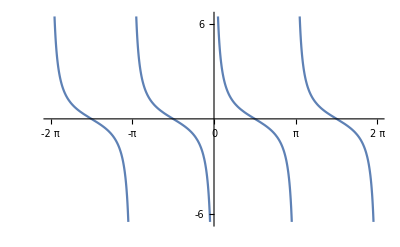

```mathematica
Plot[f[x],{x,-2π,2π},Ticks->{{-2π,-π,0,π,2π},{-6,6}}]
```

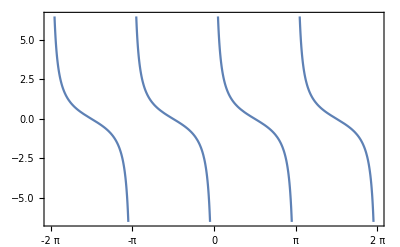

```mathematica
Plot[f[x],{x,-2 π,2 π},Sequence[Frame->True,FrameTicks->{{Automatic,None},{{(-2) Pi,-Pi,0,Pi,2 Pi},None}}]]
```

```mathematica
{Limit[f[x],x->0,Direction->"FromBelow"],
Limit[f[x],x->0,Direction->"FromAbove"]}
```

{-∞,∞}

```mathematica
list =Table[n π,{n,-2,2}]
```

{-2 π,-π,0,π,2 π}

```mathematica
Limit[f[x],x->list]
```

{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

```mathematica
{Limit[f[x],x->list, Direction->"FromBelow"],
Limit[f[x],x->list,Direction->"FromAbove"]}
```

{{-∞,-∞,-∞,-∞,-∞},{∞,∞,∞,∞,∞}}

## Difference Quotient and Table of Values

```mathematica
f[h_]:=((x+h)^2-x^2)/h
```

```mathematica
Grid[
Table[{h,FullSimplify[f[h]]},
{h,{-1,-.5,-.1,-.01,-.001,.001,.01,.05,.1,.5,1}}],
Frame->All]
```

-1 | -1+2 x
-0.5 | -0.5+2. x
-0.1 | -0.1+2. x
-0.01 | -0.01+2. x
-0.001 | -0.001+2. x
0.001 | 0.001+2. x
0.01 | 0.01+2. x
0.05 | 0.05+2. x
0.1 | 0.1+2. x
0.5 | 0.5+2. x
1 | 1+2 x

```mathematica
Limit[f[h],h->0]
```

2 x

## Exercises 4: The Limit of a Function

## Exercise 1 - Rational Function

```mathematica
f[x_]:=(x^5-1)/(x^10-1)
```

```mathematica
limitTablea[f,1]
```

{x | (x^5-1)/(x^10-1)
0 | 1.
0.5 | 0.969697
0.9 | 0.628737
0.95 | 0.563767
0.99 | 0.51256
0.995 | 0.506265
0.999 | 0.501251,x | (x^5-1)/(x^10-1)
2 | 0.030303
1.5 | 0.116364
1.1 | 0.383067
1.05 | 0.439313
1.01 | 0.487565
1.005 | 0.493766
1.001 | 0.498751}

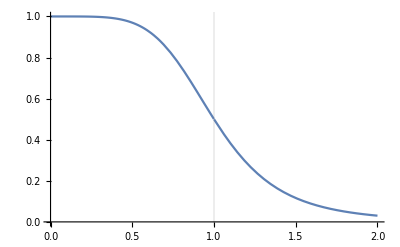

```mathematica
Plot[f[x],{x,0,2},GridLines->{{1},None}]
```

```mathematica
Limit[f[x],x->1]
```

1/2

## Exercise 2 - Trig Function Given a Table of Values

```mathematica
f[x_]:=Sin[x]/(x-Tan[x])
Grid[Table[{x,f[x]},
{x,{-1,-.5,-.1,-0.01,-.001,.001,.1,.05,.1,.5,1}}],Frame->All]//N
```

-1. | -1.50961
-0.5 | -10.3542
-0.1 | -298.302
-0.01 | -29998.3
-0.001 | -3.×10^6
0.001 | -3.×10^6
0.1 | -298.302
0.05 | -1198.3
0.1 | -298.302
0.5 | -10.3542
1. | -1.50961

```mathematica
Limit[f[x],x->0]
```

-∞

## Exercise 3 - Difference Quotient

```mathematica
f[h_]:=((2+h)^5-32)/h
limitGraph[f,0]
```

limitGraph[f,0]

```mathematica
limitTablea[f,0]
```

{x | ((x+2)^5-32)/x
-1 | 31.
-0.5 | 48.8125
-0.1 | 72.3901
-0.05 | 76.0988
-0.01 | 79.204
-0.005 | 79.601
-0.001 | 79.92,x | ((x+2)^5-32)/x
1 | 211.
0.5 | 131.313
0.1 | 88.4101
0.05 | 84.1013
0.01 | 80.804
0.005 | 80.401
0.001 | 80.08}

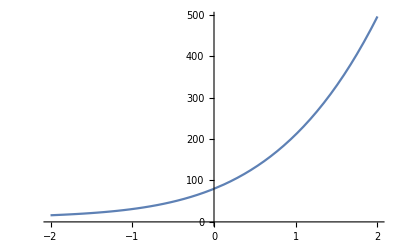

```mathematica
Plot[f[h],{h,-2,2}]
```

```mathematica
Limit[f[h],h->0]
```

80

## Exercise 4 - Where does the limit not exist?

```mathematica
f[x_]:=Piecewise[{{1+x,x<-1},{2 x^2,-1<=x<=1}},3-x]
```

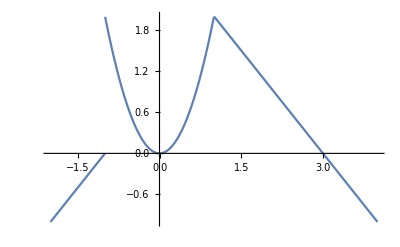

```mathematica
Plot[f[x],{x,-2,4}]
```

```mathematica
{Limit[f[x],x->-1,Direction->"FromBelow"],
Limit[f[x],x->-1,Direction->"FromAbove"]}
```

{0,2}

```mathematica
{Limit[f[x],x->1,Direction->"FromBelow"],
Limit[f[x],x->1,Direction->"FromAbove"]}
```

{2,2}

## Exercise 5 - An Application from Special Relativity

```mathematica
mass[v_]:=m0/Sqrt[1-v^2/c^2]
```

```mathematica
c=299792458;
m0 =1;
```

```mathematica
Grid[Table[{x, mass[x]},
{x,{c-1,c-.5,c-.1,c-.01,c-.001}}],
Frame->All]//N
```

2.99792×10^8 | 12243.2
2.99792×10^8 | 17314.5
2.99792×10^8 | 38716.4
2.99792×10^8 | 122432.
2.99792×10^8 | 387169.

```mathematica
Limit[mass[v],v->c,Direction->"FromBelow",
Assumptions->m0>0&&c>0]
```

∞